## Visualization

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

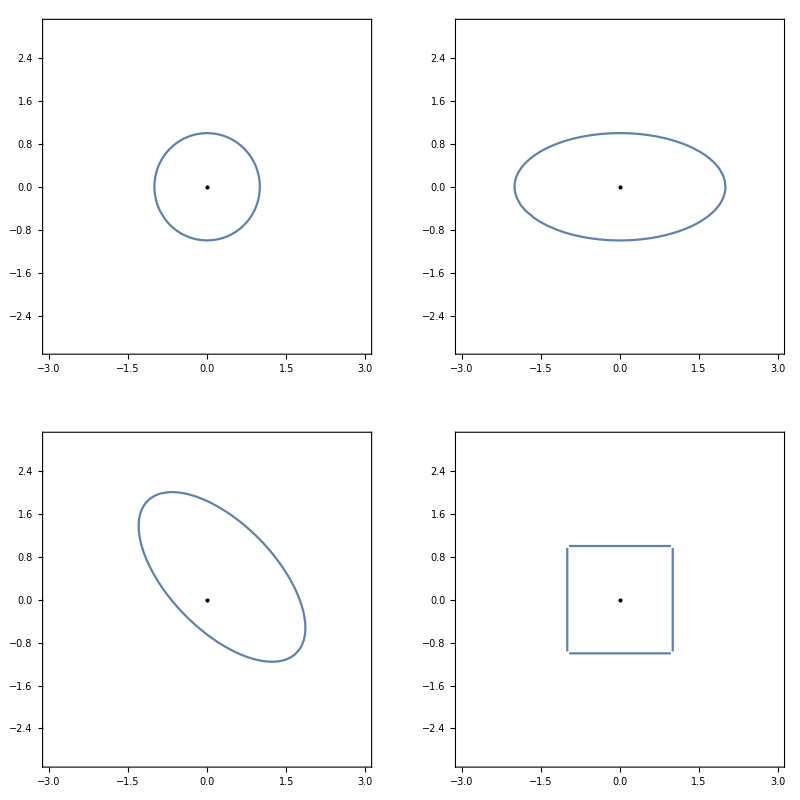

```mathematica
defVel[F1,{x,y}.{x,y}==1]
defVel[F2,{2Cos[t],Sin[t]}]
defVel[F3,ℛ[π/4].({Cos[t],2Sin[t]}+{1/2,1/10})]
defVel[F4,{{-1,-1},{1,-1},{1,1},{-1,1}}]
velocityGird=GraphicsGrid[Map[Show[{
ContourPlot[Subscript[γ, #][{x,y}]==1,{x,-3,3},{y,-3,3}],
Graphics@Point[{0,0}]
}]&,
{{F1,F2},{F3,F4}},{-1}]]
```

```mathematica
pts=RandomReal[{0,1},{5,2}]

GraphicsGrid[Map[
Plot3D[Evaluate[
Map[Function[{pt},Subscript[γ, #][{x,y}-pt]],pts]
],{x,0,1},{y,0,1},PlotRange->2,Axes->False,MeshStyle->Transparent,
ViewPoint->{0,0,-Infinity},SphericalRegion->Sphere[Automatic,4],
MaxRecursion->4]
&,
{{F1,F2},{F3,F4}},{-1}]]
```

{{0.696012,0.524879},{0.00357267,0.902216},{0.187642,0.784155},{0.555563,0.517877},{0.0735784,0.301045}}

-Graphics-

```mathematica
DiscreteArgMin[list_List]:=Position[list,Min[list],2][[1,1]]
```

```mathematica
(*pts=RandomReal[{0.1,0.9},{5,2}];*)

voronoiGrid=GraphicsGrid[Map[
Show[{
ContourPlot[
DiscreteArgMin[Map[Function[{pt},Subscript[γ, #][{x,y}-pt]],pts]]
,{x,0,1},{y,0,1},
MaxRecursion->4],
Graphics[{PointSize[0.025],Red,Point[pts]}]
}]&,
{{F1,F2},{F3,F4}},{-1}]];
```

```mathematica
GraphicsRow[{velocityGird,voronoiGrid}]
```

-Graphics-